# ChristopherWolfram/ViennaRNALink

Connecting ViennaRNA to the Wolfram Language for RNA folding

## Paclet Manifest

"Documentation"

"English"

"Guides"

"ViennaRNALink.nb"DocumentationEnglishGuidesViennaRNALink.nb

"ReferencePages"

"Symbols"

"RNAFold.nb"DocumentationEnglishReferencePagesSymbolsRNAFold.nb

"$LibViennaRNA.nb"DocumentationEnglishReferencePagesSymbols$LibViennaRNA.nb

"Tutorials"

"Kernel"

"LibViennaRNA.wl"KernelLibViennaRNA.wl

"RNAFold.wl"KernelRNAFold.wl

"Utilities.wl"KernelUtilities.wl

"ViennaRNALink.wl"KernelViennaRNALink.wl

"LibraryResources"

"Linux-x86-64"

"libRNA.so"LibraryResourcesLinux-x86-64libRNA.so

"MacOSX-ARM64"

"libRNA.dylib"LibraryResourcesMacOSX-ARM64libRNA.dylib

"MacOSX-x86-64"

"libRNA.dylib"LibraryResourcesMacOSX-x86-64libRNA.dylib

"LICENSE"LICENSE

"Notes"

"viennaRNA-1.nb"NotesviennaRNA-1.nb

"viennaRNAPaclet-1.nb"NotesviennaRNAPaclet-1.nb

"PacletInfo.wl"PacletInfo.wl

"ResourceDefinition.nb"ResourceDefinition.nb

"Tests"

"RNAFold.wlt"TestsRNAFold.wlt

## Web Content

### Headline Image

### Basic Description

ViennaRNALink uses the foreign function interface (FFI) to connect Wolfram Language to ViennaRNA, a package used for RNA structure prediction.

### Details

ViennaRNA is developed by Ivo Hofacker, Peter Stadler, Walter Fontana, Stefan Wuchty, Stephan Bernhart, Ulli Mueckstein, Ronny Lorenz, and the Institute for Theoretical Chemistry of the University of Vienna.

### Primary Context

ChristopherWolfram`ViennaRNALink`

### Main Guide Page

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
```

```mathematica
Needs["ChristopherWolfram`ViennaRNALink`"];
```

### Basic Examples

Fold an RNA sequence:

```mathematica
RNAFold["GAGUAGUGGAACCAGGCUAUGUUUGUGACUCGCAGACUAACA"]
```

BioSequence[…]

Plot it:

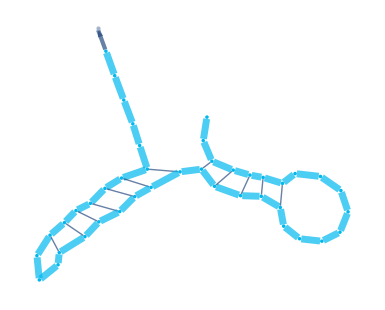

```mathematica
BioSequencePlot[%]
```

### Scope

Get the minimum free energy:

```mathematica
RNAFold["GAGUAGUGGAACCAGGCUAUGUUUGUGACUCGCAGACUAACA","MinimumFreeEnergy"]
```

-8.8 kcal_th/mol

Fold random RNA sequences:

```mathematica
Table[BioSequencePlot[RNAFold[StringJoin[RandomChoice[{"G","U","A","C"},100]]]],10]
```

-Graphics-

Fold a long sequence:

```mathematica
Needs["ChristopherWolfram`ViennaRNALink`"]
```

```mathematica
BioSequencePlot[RNAFold[StringJoin[RandomChoice[{"G","U","A","C"},1000]]]]
```

-Graphics-

## Source & Additional Information

### Creator

Christopher Wolfram

### Source Control Repository

https://github.com/chriswolfram/ViennaRNALink

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

RNA

RNA folding

Vienna RNA

ViennaRNA

Secondary structure

Structure prediction

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Original Source References and Attributions

GitHub - chriswolfram/ViennaRNALink

TBI - ViennaRNA Package 2

### Links

Link to other related material

### Compatibility

#### Wolfram Language Version

14+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

Wolfram Language system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

Wolfram Language built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

Paclet dependenciesDisclosuresPacletDependenciesChoose this option if your paclet directly installs or updates any additional paclets. Paclets that are included with the Wolfram system do not require a disclosure.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

Windows builds are experimental, and Intel Mac builds have not been tested.

On macOS, the first time the paclet is used after being installed, there may be a dialog about "unidentified developers". This dialog can be suppressed by going to System Settings → Privacy & Security and selecting "Allow Anyway".